```mathematica
BodePlot[TransferFunctionModel[{s,s^2,s^3}//.s->I 2 π f, f]]
```

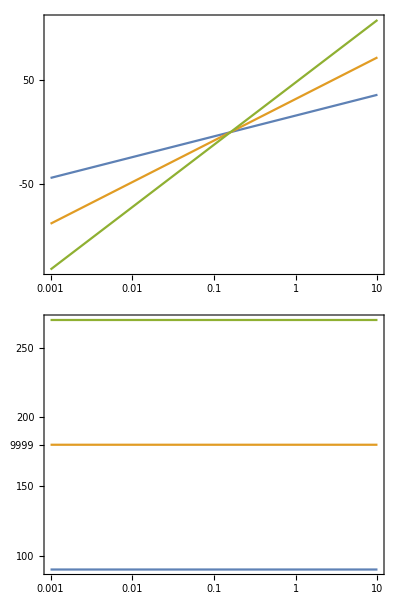

```mathematica
20 Log[10, Abs[{s, s^2, s^3}]]//.s->I 2 Pi {f, 10 f}
```

{{(20 Log[2 π Abs[f]])/Log[10],(20 Log[20 π Abs[f]])/Log[10]},{(20 Log[4 π^2 Abs[f]^2])/Log[10],(20 Log[400 π^2 Abs[f]^2])/Log[10]},{(20 Log[8 π^3 Abs[f]^3])/Log[10],(20 Log[8000 π^3 Abs[f]^3])/Log[10]}}

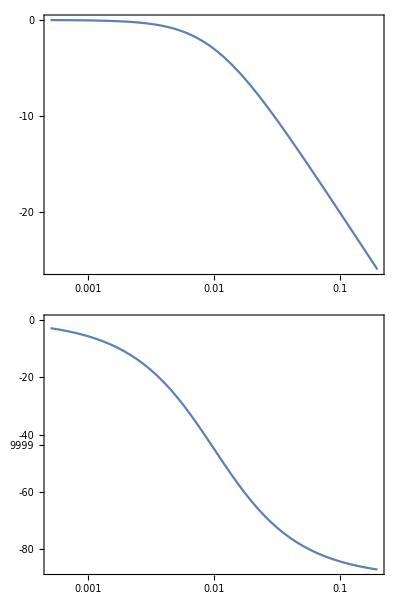

```mathematica
t=100;
BodePlot[TransferFunctionModel[{1/(1+s*t)} , s]]
```

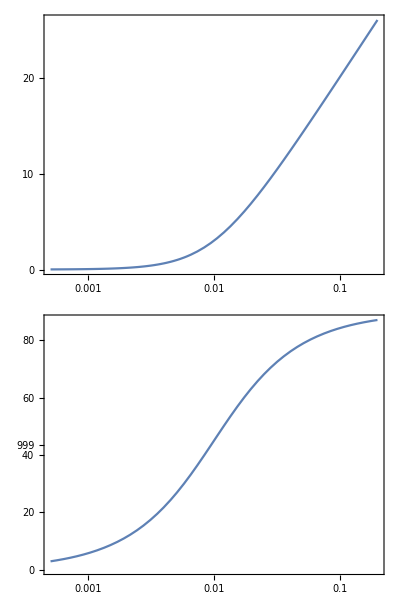

```mathematica
t=100;
BodePlot[TransferFunctionModel[{1+s*t} , s]]
```

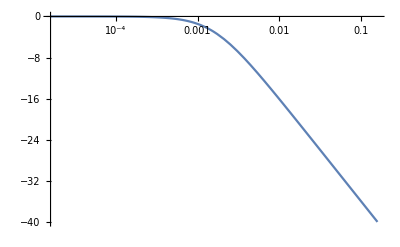

```mathematica
t=100;
LogLinearPlot[20 Log[10, Abs[1/(1+s t)]]//.s->I 2 Pi f,{f, 1/(2 Pi t 100), 1/(2 Pi t) 100}]
```

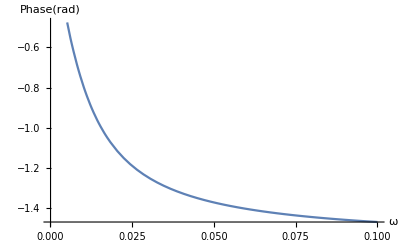

```mathematica
T=100;
Plot[-ArcTan[T*ω],{ω,0.0001,0.1},AxesLabel->{"ω","Phase(rad)"}]
```

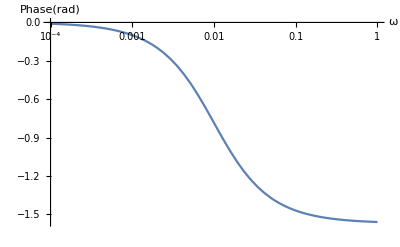

```mathematica
T=100;
LogLinearPlot[-ArcTan[T*ω],{ω,0.0001,1},AxesLabel->{"ω","Phase(rad)"}]
```

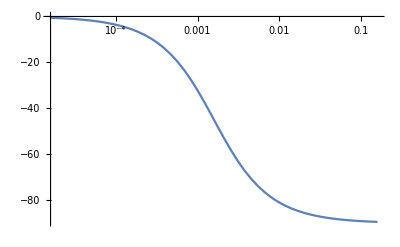

```mathematica
t = 100;
LogLinearPlot[Arg[1/(1+s t)] 57.3//.s->I 2 Pi f,{f,1/(2 Pi t 100), 1/(2 Pi t) 100}]
```

```mathematica
Arg[1+1 I]
```

π/4

```mathematica
ArcTan[1]
```

π/4

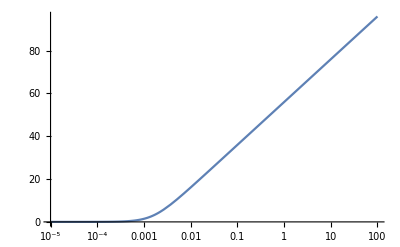

```mathematica
t = 100;
LogLinearPlot[20 Log[10, Abs[1+2 Pi f I t]],{f,0.00001,100}]
```

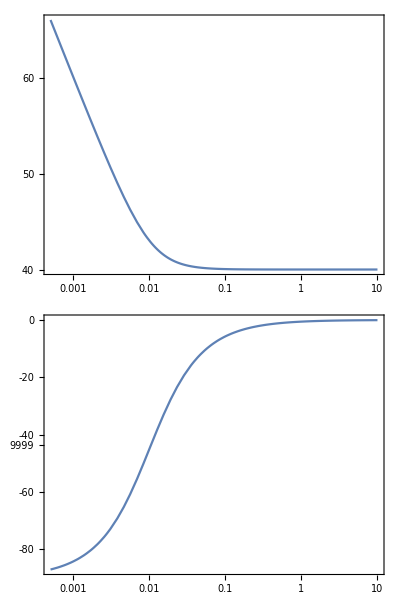

```mathematica
Kp = 1;
Ki = 1;
t =100;
BodePlot[TransferFunctionModel[(1+s t)/s,s]]
```

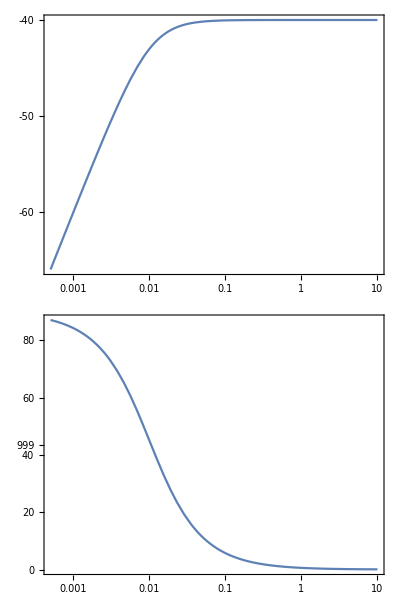

```mathematica
t =100;
BodePlot[TransferFunctionModel[s/(1+s t),s]]
```

```mathematica
Kp = 100;
Ki = 1;
BodePlot[TransferFunctionModel[Ki (Kp/Ki s +1)/s,s]]
```

-Graphics-

```mathematica
Manipulate[
BodePlot[TransferFunctionModel[Ki (Kp/Ki s +1)/s,s]],{Kp, 0.0001, 100},{Ki, 0.0001, 100}]
```

^6